# Statistische Mechanik Bonusblatt

```mathematica
ClearAll["Global`*"]
```

## Helpful Functions

This formats quantities with errors

```mathematica
f[{a_,b_}]:=NumberForm[SetAccuracy[a±b,Accuracy@SetPrecision[b,2]],ExponentFunction->(Null&)]//Quiet
```

## Random Walk

```mathematica
NExperiments = 1000000;
```

```mathematica
L=200;
```

```mathematica
randomWalkData=Import[NotebookDirectory[]<>"randomWalk.csv"][[All,1;;-2]];
```

```mathematica
randomWalkDataProcessed = Transpose[{Range[0,L], Around[#[[1]],#[[2]]/Sqrt[NExperiments]]&/@Transpose[randomWalkData]}];
```

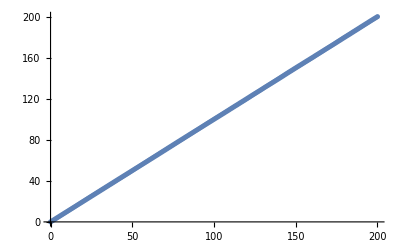

```mathematica
ListPlot[randomWalkDataProcessed]
```

```mathematica
Transpose[{Range[0,L], f[{#[[1]],#[[2]]/Sqrt[NExperiments]}]&/@Transpose[randomWalkData]}]//TeXForm//CopyToClipboard
```

## Random Avoiding Walk

```mathematica
NAvoidingExperiments = 1000000;
LAvoiding = 40;
```

```mathematica
randomAvoidingWalkData=Import[NotebookDirectory[]<>"randomAvoidingWalk.csv"][[All,1;;-2]]
```

{{0,1,2.72338,4.16704,5.64786,7.04189,8.44765,9.80346,11.1628,12.4847,13.8121,15.1071,16.4028,17.6584,18.9248,20.1715,21.4191,22.6412,23.8576,25.0642,26.2625,27.4479,28.6355,29.7908,30.9522,32.1005,33.2361,34.365,35.4922,36.5944,37.7133,38.8101,39.8984,40.9799,42.0572,43.1132,44.1604,45.2115,46.2388,47.2591,48.2849},{0,0,0.960981,2.45914,3.62292,4.86384,6.01453,7.198,8.33793,9.49103,10.6094,11.7357,12.8371,13.9456,15.0422,16.1499,17.2428,18.3379,19.4363,20.5366,21.6202,22.6859,23.7489,24.8195,25.9071,26.9756,28.0287,29.0756,30.1459,31.1954,32.2861,33.3526,34.4239,35.5309,36.5968,37.674,38.7527,39.8445,40.9208,42.0461,43.1652}}

```mathematica
randomAvoidingWalkDataProcessed = Transpose[{Range[0,LAvoiding], Around[#[[1]],#[[2]]/Sqrt[NAvoidingExperiments]]&/@Transpose[randomAvoidingWalkData]}];
```

```mathematica
Transpose[{Range[0,LAvoiding], f[{#[[1]],#[[2]]/Sqrt[NAvoidingExperiments]}]&/@Transpose[randomAvoidingWalkData]}]//TeXForm//CopyToClipboard
```

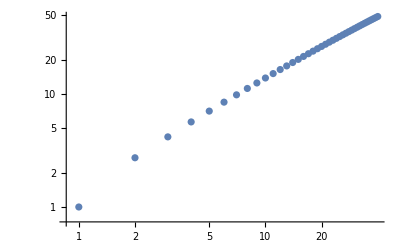

```mathematica
ListLogLogPlot[randomAvoidingWalkDataProcessed]
```